# Mathematica (Wolfram Language)

## Symbolic mathematics and computer algebra

Will Pazner

## History

Created by physicist Stephen Wolfram

First version released in 1988

Pioneered the “notebook interface” (long before Jupyter, etc.)

Propriety/closed source (costs $$$$)

### What is it?

Mathematica is a computer algebra system

Can be used for symbolic/mathematical computations and manipulations

Has an extensive library of functionality

Calculus, abstract algebra, differential equations, visualization, graphics, statistics, graph computations, neural networks, etc.

Also a “general purpose” programming language

## Today’s lecture

“Using Mathematica”

Writing simple programs

Learning the syntax of the language

Using the built-in functionality to solve problems

Next lecture: understanding the internal structure of the language

## The notebook interface

Very similar to Jupyter notebooks

Enter code/expressions in a cell

Shift-return (or enter on the numeric keypad) evaluates the expression

The output is shown below the input cell

-Graphics-

```mathematica
1+2
```

## Simple arithmetic

The usual operations work:

```mathematica
1+1
```

Note: division of integers gives rational numbers not floating point:

```mathematica
2/3
```

Numbers with decimal points are interpreted as inexact (i.e. double precision floating point)

```mathematica
2./3.
```

Group expressions using parentheses. Multiplication can be perform by adding a space (a gray x will appear):

```mathematica
2*3
```

```mathematica
2 3
```

## More computations

There are a huge number of mathematical functions built in:

```mathematica
4!
```

Sin, Cos, Log, Exp, Gamma, Erf

Note:

All built-ins in Mathematica begin with a capital letter

Even constants, e.g. Pi, E, and I

This leaves all lowercase-beginning identifiers for user code

## Function call syntax

Unlike in Julia, functions are called with square brackets

Examples:

```mathematica
Sin[Pi]
```

```mathematica
Exp[1]
```

```mathematica
Log[E]
```

As in Julia, arguments are separated by commas:

```mathematica
ArcTan[1,1]
```

## Variables and expressions

Here we begin to see what makes Mathematica different

Unlike in Julia, variables may be used before they are assigned a value

Mathematica will manipulate the expression with variables held in an unevaluated form

```mathematica
x+x
```

## Mathematical expressions

Using variables in this way lets us manipulate mathematical objects such as equations and polynomials

Note: using some shortcuts, you can use “fancy” notation in input cells (e.g. superscripts for powers, fractions for division, etc.)

```mathematica
a*x^2+b*x+c
```

```mathematica
a x^2+b x+c
```

## Plotting

Expressions defining functions in one variable can be plotted:

```mathematica
Plot[x,{x,0,2}]
```

The syntax {x,0,1} defines a list (similar to an array in Julia).
Lists can contain anything, and can be arbitrarily nested

```mathematica
{x,0,1}
```

We will see later how to access and manipulate lists. For now we will just use simple lists to define the axes.

## More plotting

The plotting and visualization functionality of Mathematica is very advanced
You can read the built-in documentation to learn more
Some examples:

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

## Using Mathematica for calculus

Mathematica is what Wolfram Alpha is based on
(You may be familiar from Math 1A...)

There is very powerful built-in differentiation and integration of expressions:

```mathematica
Sqrt[x]Tanh[Sin[x]]
```

```mathematica
D[Sqrt[x]Tanh[Sin[x]],x]
```

Integrate can be used to compute indefinite integrals

```mathematica
Integrate[Sqrt[x]Cos[x]Sech[Sin[x]]^2+Tanh[Sin[x]]/2/Sqrt[x],x]
```

Providing bounds of integration in the form of a list (just like in plotting) can be used to compute definite integrals

```mathematica
Integrate[Sqrt[x]Cos[x]Sech[Sin[x]]^2+Tanh[Sin[x]]/2/Sqrt[x],{x,0,Pi/2}]
```

If we want to use quadrature instead, that is also available

```mathematica
NIntegrate[Sqrt[x]Cos[x]Sech[Sin[x]]^2+Tanh[Sin[x]]/2/Sqrt[x],{x,0,Pi/2}]
```

Numerical (approximate results) can be obtained using the N function

```mathematica
N[Sqrt[Pi/2] Tanh[1]]
```

```mathematica
N[Sqrt[Pi/2] Tanh[1],30]
```

If we want to be fancy, we can use mathematical notation in our code:

```mathematica
N[√(π/2)Tanh[1],30]
```

```mathematica
Plot[Sqrt[x]Cos[x]Sech[Sin[x]]^2+Tanh[Sin[x]]/2/Sqrt[x],{x,0,4Pi}]
```

## Creating and assigning variables

Variables are assigned using the equal sign = (Set)

lhs = rhs

will evaluate the expression ‘rhs’ and assign the result to ‘lhs’. The right-hand side can be any Mathematica expression

```mathematica
x=Pi^2
```

```mathematica
N[x]
```

```mathematica
2 x^2+x
```

Variables can be unset using Clear

```mathematica
Clear[x]
```

```mathematica
x
```

## Lists

As we saw, lists can be created using braces

```mathematica
mylist={3,8,4}
```

We can perform arithmetic operations on lists

```mathematica
mylist+1
```

```mathematica
mylist*2
```

The entries of a list are accessed using double-brackets (or the special notation ⟦ ⟧)
The entries are indexed starting with one

```mathematica
mylist[[1]]
```

```mathematica
mylist⟦3⟧
```

We can also index a list using a list

```mathematica
mylist⟦{1,2}⟧
```

Lists can be mutated this way

```mathematica
mylist⟦3⟧=Pi
```

```mathematica
mylist
```

## Recall

There are four kinds of bracketing in Mathematica:

(Parentheses) for grouping mathematical expressions

```mathematica
2+3*4
```

```mathematica
(2+3)*4
```

[Square brackets] for functions calls

```mathematica
Sin[Pi]
```

{Braces} for lists

```mathematica
{1,2,3}
```

[[Double brackets]] for indexing

```mathematica
{7,8,9}[[2]]
```

## Creating Lists

Simple ranges can be constructed using Range

```mathematica
Range[10]
```

```mathematica
Range[4,10]
```

```mathematica
Range[4,10,2]
```

Much more flexible is Table, which allows for the creation of lists using expressions

```mathematica
Table[i,{i,10}]
```

```mathematica
Table[i^2,{i,1,10}]
```

```mathematica
Table[i^2/i!,{i,10}]
```

Table can also be used to create matrices (which are represented as lists of lists)

```mathematica
mat=Table[i+j,{i,1,10},{j,1,10}]
```

Matrices can be displayed nicely using MatrixForm

```mathematica
MatrixForm[mat]
```

Note: functions can also be evaluated using postfix notation with the // operator

```mathematica
mat//MatrixForm
```

## Interactivity

One of Mathematica’s most powerful features is its interactivity

Consider plotting a set of parabolas

y=(x-a)^2

parameterized by the value a

We begin by choosing a “representative” set

```mathematica
parabolas=Table[(x-a)^2,{a,-2,2,1/2}]
```

Plotting these functions gives us some insight

```mathematica
Plot[parabolas,{x,-6,6},PlotRange->{0,60}]
```

More useful is manipulating the parameter interactively

```mathematica
Manipulate[Plot[(x-a)^2,{x,-6,6},PlotRange->{0,60}],{a,-2,2}]
```

We can use manipulate to understand e.g. frequency and amplitude of waves

```mathematica
Manipulate[
Plot[a*Sin[ω*x],{x,0,2π},PlotRange->{-3,3}],
{a,1,3},
{ω,1,10}
]
```

## Algebraic manipulation and simplification

This is one of the most powerful features of Mathematica

```mathematica
Factor[1+2x+x^2]
```

```mathematica
Expand[(1+x+3y)^4]
```

In particular, Simplify is one of the most useful single functions

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

Sometimes FullSimplify can simplify more complicated expressions (using an expanded set of rules)

```mathematica
Simplify[Gamma[x]Gamma[1-x]]
```

```mathematica
FullSimplify[Gamma[x]Gamma[1-x]]
```

```mathematica
myexpr=(x-1)^2(2+x)/((1+x)(x-3)^2)
```

```mathematica
Apart[myexpr]
```

The percent symbol can be used as a shortcut for the output of the last expression

```mathematica
Together[%]
```

```mathematica
Factor[%]
```

```mathematica
ExpandAll[%]
```

## Substitution rules

Given an expression such as:

```mathematica
myexpr=a*x^2+b*x+c
```

We can evaluate this expression with the variables replaced by numbers (or any other expressions) using substitution rules

The replacement operator is typed slash-dot, and rules are typed ->

```mathematica
myexpr/.x->3
```

Multiple substitutions can be made at once using lists of rules

```mathematica
myexpr/.{x->3,a->1,b->2,c->0}
```

## More algebraic manipulations

Simplify tends not to make assumptions about the variables

```mathematica
Simplify[Sqrt[x^2]]
```

Assumptions can be provided as a second argument to Simplify:

```mathematica
Simplify[Sqrt[x^2],x≥0]
```

Algebraic expressions can be analyzed programmatically:

```mathematica
myexpr=Expand[(1+3x+4y^2)^2]
```

```mathematica
Coefficient[myexpr,x]
```

```mathematica
Exponent[myexpr,y]
```

```mathematica
myexpr⟦3⟧
```

```mathematica
r=(1+x)/(2(2-y))
```

```mathematica
Numerator[r]
```

```mathematica
Denominator[r]
```

```mathematica
r=.
```

## Example: binomial theorem

Recall the binomial theorem:

(x+y)^n=∑_(k=0)^n (n
k)x^k y^(n-k)

Mathematica immediately simplifies using this identity:

```mathematica
binom=Sum[Binomial[n,k] x^k y^(n-k),{k,0,n}]
```

We can evaluate for a specific n using a replacement rule

```mathematica
binom/.n->10
```

```mathematica
%//Expand
```

## More calculus and series

Mathematica can easily compute partial and repeated derivatives

```mathematica
D[x^n,x]
```

```mathematica
D[x^n,{x,2}]
```

```mathematica
D[x^n,{x,5}]
```

```mathematica
D[Sin[x]Cos[y],{{x,y}}]
```

Finite and infinite sums can be computed using Sum

```mathematica
Sum[x^i/i,{i,1,10}]
```

```mathematica
Sum[1/i^4,{i,1,Infinity}]
```

```mathematica
Sum[1/2^i,{i,0,Infinity}]
```

```mathematica
Product[(x+i),{i,1,5}]
```

## Equations

Just like in Julia, equality is tested with ==

```mathematica
x=3
```

3

```mathematica
x==4
```

False

```mathematica
x==3
```

True

```mathematica
Clear[x]
```

Equations are themselves Mathematica expressions

```mathematica
myeqn=a x^2+b x+c==0
```

c+b x+a x^2==0

Equations can be solved using Solve

```mathematica
Solve[myeqn,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[x^2+2x-7==0,x]
```

{{x→-1-2 √2},{x→-1+2 √2}}

```mathematica
N[%]
```

{{x→-3.82843},{x→1.82843}}

NSolve (for “numeric solve”) will look for numeric rather than symbolic solutions

```mathematica
NSolve[x^2+2x-7==0,x]
```

{{x→-3.82843},{x→1.82843}}

For linear, quadratic, cubic, and quartic polynomials, Mathematica will always give a closed-form solution

```mathematica
Solve[x^4-5x^2-3==0,x]
```

{{x→-ⅈ √(1/2 (-5+√37))},{x→ⅈ √(1/2 (-5+√37))},{x→-√(1/2 (5+√37))},{x→√(1/2 (5+√37))}}

Some equations do not admit closed-form solutions

```mathematica
Solve[2-4x+x^5==0,x]
```

{{x→Root-1.52Root[2-4 #1+#1^5&,1]-1.518512152784912},{x→Root0.508Root[2-4 #1+#1^5&,2]0.5084994846573327},{x→Root1.24Root[2-4 #1+#1^5&,3]1.2435963905735432},{x→Root-0.117-1.44 ⅈRoot[2-4 #1+#1^5&,4]-0.11679186122298207},{x→Root-0.117+1.44 ⅈRoot[2-4 #1+#1^5&,5]-0.11679186122298207}}

```mathematica
NSolve[2-4x+x^5==0,x]
```

{{x→-1.51851},{x→-0.116792-1.43845 ⅈ},{x→-0.116792+1.43845 ⅈ},{x→0.508499},{x→1.2436}}

You can also solve for simultaneous systems of equations

```mathematica
Solve[{a x+y==0,2 x+(1-a) y==1},{x,y}]
```

## Differential equations

Mathematica can find analytical solutions to many differential equations, both initial value problems and boundary value problems

The function DSolve looks for solutions to differential equations

```mathematica
DSolve[y'[x]==a y[x]+1,y,x]
```

{{y→Function[{x},-1/a+ⅇ^(a x) C[1]]}}

We did not specify an initial condition, so the solution has a constant. Specifying the initial condition eliminates the constant

```mathematica
soln=DSolve[{y'[x]==a y[x]+1,y[0]==1},y,x]
```

{{y→Function[{x},(-1+ⅇ^(a x)+a ⅇ^(a x))/a]}}

```mathematica
y[x]/.soln
```

{(-1+ⅇ^(a x)+a ⅇ^(a x))/a}

```mathematica
y[x]/.soln/.a->1
```

{-1+2 ⅇ^x}

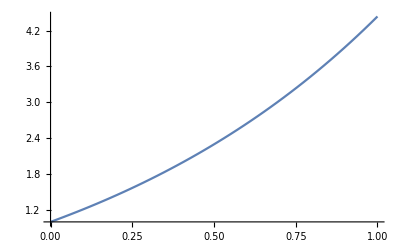

```mathematica
Plot[y[x]/.soln/.a->1,{x,0,1}]
```

We can solve a boundary value problem:

```mathematica
DSolve[{y''[x]==-Sin[x],y[0]==0,y[1]==0},y,x]
```

{{y→Function[{x},-x Sin[1]+Sin[x]]}}

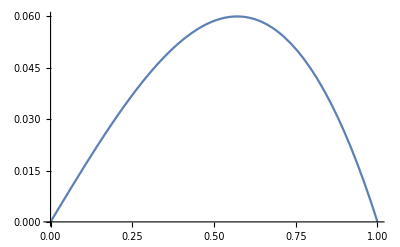

```mathematica
Plot[y[x]/.%,{x,0,1}]
```

## Set and SetDelayed

Up until now, we have assigned expressions to variables using =, which is called Set

Whenever we write lhs = rhs, the rhs is evaluated immediately

Sometimes we don’t want to evaluate the rhs immediately. Instead, we want to wait until we encounter lhs somewhere else in our program. When we encounter lhs, it is replaced by rhs and only then evaluated

This is denoted SetDelayed, and is written :=

For example, we will use Set for x, and SetDelayed for y

```mathematica
x=Random[]
y:=Random[]
```

0.456014

```mathematica
x
```

0.119744

```mathematica
x
```

0.119744

```mathematica
x
```

0.119744

```mathematica
y
```

0.494581

```mathematica
y
```

0.0242098

```mathematica
y
```

0.974407

## Defining functions

Functions are just another type of expression in Mathematica

Their argument lists take the form of patterns. We will discuss patterns in more depth in the next lecture

For now, we will make use of one kind of pattern: x_
which matches any expression and calls it x.
For example:

```mathematica
addOne[x_]:=x+1
```

This function can be called with any kind of argument. That argument will be called x in the body of the function, which gives a result by adding one

```mathematica
addOne[2]
```

3

```mathematica
addOne[{3,4,5}]
```

{4,5,6}

There are much more sophisticated patterns than just “match any expression.” We will cover these later.

Suppose we want to recursively compute the factorial
Base case: fac(0) = 1
Recursive definition: fac(n) = n*fac(n-1)

This is simple to define in Mathematica.
We begin with the base case

```mathematica
fac[0]:=1
```

Now, fac[0] will evaluate to 1

```mathematica
fac[0]
```

1

We don’t have a rule for the general case, so fac[n] will remain unevaluated:

```mathematica
fac[1]
```

fac[1]

Defining the general case:

```mathematica
fac[n_]:=n*fac[n-1]
```

```mathematica
fac[1]
```

1

```mathematica
fac[10]
```

3628800

```mathematica
10!
```

3628800

Let’s do a similar exercise with the Fibonacci sequence:
F_0=0
F_1=1
F_n=F_(n-1)+F_(n-2)

```mathematica
fib[0]:=0
fib[1]:=1
fib[n_]:=fib[n-1]+fib[n-2]
```

```mathematica
fib[10]
```

55

Of course, Mathematica also has this built in, so we can check our work...

```mathematica
Fibonacci[10]
```

55

## Solving recurrence relations

Suppose we have the recurrence relation

a_0=2
a_1=3
a_n=7 a_(n-1)-10 a_(n-2)

We can easily create a function to recursively evaluate this sequence

```mathematica
a[0]:=2
a[1]:=3
a[n_]:=7a[n-1]-10a[n-2]
```

```mathematica
a[10]
```

What if we want to know a general (non-recursive formula)?
First, concentrate on the recursive definition a_n=7 a_(n-1)-10 a_(n-2) (ignoring initial conditions)
Equivalently,

a_n-7 a_(n-1)+10 a_(n-2)=0

We can solve this recurrence by making the ansatz that a_nis given by r^n for some r
In that case,

r^(n-2)(r^2-7r+10)=0

So, we look for solutions to this equation.

```mathematica
Factor[r^2-7r+10]
```

So, r=5 and r=2 satisfy this relationship.
The general solution will be given by a_n=c*5^n+d*2^n

We can easily solve the system of equations to find the values of c and d.
But we can also let Mathematica help...

```mathematica
expr=c*5^n+d*2^n
case0=expr/.n->0
case1=expr/.n->1
```

```mathematica
soln=Solve[{case0==2,case1==3},{c,d}]
```

Let’s check our formula

```mathematica
expr/.soln⟦1⟧
```

```mathematica
(expr/.soln⟦1⟧/.n->7 )==a[7]
```

ClearAll deletes all the definitions we made for a

```mathematica
ClearAll[a]
```

Mathematica can also solve the recurrence directly using RSolve

```mathematica
RSolve[{a[0]==2,a[1]==3,a[n]==7a[n-1]-10a[n-2]},a,n]
```

## More complicated functions and local variables

Sometimes we want to introduce local variables in a function for intermediate values in long calculations

This can be achieved using Module

```mathematica
Module[{x,y,z},
(* 
 (This is a comment by the way)
x, y, and z are declared as local variables
*)
x=1;
y=x+1;
z=y*2;
Print[{x,y,z}];
]
```

{1,2,4}

```mathematica
Print[{x,y,z}]
```

{x,y,z}

Mathematica also has other scoping mechanisms (i.e. for creating variables with local scope)
See e.g. Block, With

For our uses, Module is sufficient

## Functional style programming

Mathematica is a multi-paradigm programming language

It supports both functional and imperative programming, but functional constructs are often very natural

For example, applying a function f to a list is known as mapping f over the list

```mathematica
mylist=Table[i^2,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Map[Sqrt,mylist]
```

{1,2,3,4,5,6,7,8,9,10}

Map is considered so important in Mathematica it has its own syntax

```mathematica
Sqrt/@mylist
```

{1,2,3,4,5,6,7,8,9,10}

We can define more complicated functions if we want

```mathematica
f[x_]:=Sin[Sqrt[x]+x^(2/3)]
```

```mathematica
Map[f,mylist]
```

{Sin[2],Sin[2+2 2^(1/3)],Sin[3+3 3^(1/3)],Sin[4+4 2^(2/3)],Sin[5+5 5^(1/3)],Sin[6+6 6^(1/3)],Sin[7+7 7^(1/3)],Sin[24],Sin[9+9 3^(2/3)],Sin[10+10 10^(1/3)]}

Sometimes we want to create an anonymous function so that we don’t need to name it

```mathematica
Map[Sin[Sqrt[#]+#^(2/3)]&,mylist]
```

{Sin[2],Sin[2+2 2^(1/3)],Sin[3+3 3^(1/3)],Sin[4+4 2^(2/3)],Sin[5+5 5^(1/3)],Sin[6+6 6^(1/3)],Sin[7+7 7^(1/3)],Sin[24],Sin[9+9 3^(2/3)],Sin[10+10 10^(1/3)]}

Here # indicates the argument, and & tells Mathematica that the preceding expression is a function

This notation can easily become hard to read, so be careful

```mathematica
mylist2=Sin[Sqrt[#]+#^(2/3)]&/@mylist
```

{Sin[2],Sin[2+2 2^(1/3)],Sin[3+3 3^(1/3)],Sin[4+4 2^(2/3)],Sin[5+5 5^(1/3)],Sin[6+6 6^(1/3)],Sin[7+7 7^(1/3)],Sin[24],Sin[9+9 3^(2/3)],Sin[10+10 10^(1/3)]}

```mathematica
Map[N,mylist2]
```

{0.909297,-0.98152,0.864203,-0.798516,0.832447,-0.930128,0.999555,-0.905578,0.525735,0.128068}

## More functional programming

Recall our list

```mathematica
mylist
```

{1,4,9,16,25,36,49,64,81,100}

We can apply filters to the list using Select

```mathematica
Select[mylist,EvenQ]
```

{4,16,36,64,100}

We can combine this with anonymous functions

```mathematica
Select[mylist,#>20&]
```

{25,36,49,64,81,100}

Sometimes we want to apply a function to a list for its side-effect rather than its return-value

For this we have Scan

```mathematica
Scan[Print[Sqrt[#]]&,mylist]
```

1

2

3

4

5

6

7

8

9

10

There are a ton more functional programming facilities in Mathematica

See e.g. Nest, Fold, Apply

```mathematica
mylist=RandomInteger[{1,50},20]
```

Can we get the sum of all of these entries?

```mathematica
Plus[mylist]
```

```mathematica
Plus[{1,2,3}]
```

```mathematica
Plus[1,2,3]
```

```mathematica
Apply[Plus,mylist]
```

```mathematica
Total[mylist]
```

## Procedural control flow

Mathematica also has procedural control flow (perhaps more familiar from e.g. Julia)

```mathematica
x=RandomInteger[200]
If[EvenQ[x],
Print["x is even!"],
Print["x is odd!"]
]
```

172

x is even!

Which can be used for many if-else clauses

```mathematica
Which[
Mod[x,2]==0,Print["x mod 2 == 0"],
Mod[x,3]==0,Print["x mod 3 == 0"],
Mod[x,4]==0,Print["x mod 4 == 0"],
Mod[x,5]==0,Print["x mod 5 == 0"],
Mod[x,6]==0,Print["x mod 6 == 0"],
True,Print["I give up..."]
]
```

x mod 2 == 0

The simplest loop is the Do loop, which repeats the contents n times

```mathematica
Do[
x=RandomInteger[200];
If[EvenQ[x],
Print["x is even!"],
Print["x is odd!"]
],
10
]
```

x is even!

x is odd!

x is odd!

x is odd!

x is even!

x is odd!

x is odd!

x is odd!

«1 more identical outputs»

x is even!

We also have traditional for loops

```mathematica
For[i=0,i<10,i++,
Print["Iteration ",i];
x=RandomInteger[200];
If[EvenQ[x],
Print["x is even!"],
Print["x is odd!"]
]
]
```

Iteration 0

x is even!

Iteration 1

x is even!

Iteration 2

x is even!

Iteration 3

x is even!

Iteration 4

x is odd!

Iteration 5

x is even!

Iteration 6

x is odd!

Iteration 7

x is odd!

Iteration 8

x is odd!

Iteration 9

x is odd!

## Application: merge sort

Merge sort is a recursive algorithm
Given a list, we:
1. find a midpoint
2. split the list at its midpoint into a left list and right list
3. sort the left and right lists using merge sort (recursion)
4. merge the two lists

```mathematica
mergeSort[theList_]:=Module[{midpt,left,right},
If[Length[theList]≥2,
midpt=Ceiling[Length[theList]/2];
left=theList⟦1;;midpt⟧;
right=theList⟦midpt+1;;⟧;
merge[mergeSort[left],mergeSort[right]],
(* If there is only one item, the list is sorted *)
theList]
]
```

```mathematica
merge[left_,right_]:=Module[{ileft,iright},
ileft=1;
iright=1;
Table[
Which[
ileft>Length[left],right⟦iright++⟧,
iright>Length[right],left⟦ileft++⟧,
left⟦ileft⟧<right⟦iright⟧,left⟦ileft++⟧,
True,right⟦iright++⟧
],
{Length[left]+Length[right]}]
]
```

```mathematica
unsorted=Table[RandomInteger[200],20]
```

{163,43,41,80,152,58,113,106,125,132,89,33,157,22,28,11,27,45,83,101}

```mathematica
mergeSort[unsorted]
```

{11,22,27,28,33,41,43,45,58,80,83,89,101,106,113,125,132,152,157,163}

```mathematica
unsorted//mergeSort
```

{11,22,27,28,33,41,43,45,58,80,83,89,101,106,113,125,132,152,157,163}

The runtime complexity of merge sort is given by the recurrence
t(n)=2t(n/2)+O(n)

```mathematica
RSolve[t[n]==2t[n/2]+n,t,n]
```

{{t→Function[{n},(n C[1])/2+(n Log[n])/Log[2]]}}

The runtime complexity is n log(n)

## Functional-style merge sort

```mathematica
functionalMergeSort[{}]:={}
functionalMergeSort[{x_}]:={x}
functionalMergeSort[theList_]:=Module[{midpt=Ceiling[Length[theList]/2]},
Apply[merge,
Map[functionalMergeSort,
{theList⟦1;;midpt⟧,theList⟦midpt+1;;⟧},1]
]
]
```

```mathematica
functionalMergeSort[unsorted]
```

{11,22,27,28,33,41,43,45,58,80,83,89,101,106,113,125,132,152,157,163}

## Finding all primes less than n

Algorithm known as the Sieve of Eratosthenes

Choose a number n
We will find all primes less than n
1. List all numbers 2 through n
2. Starting with, p=2, mark all multiples of p, beginning with p^2
	i.e. mark p^2, p(p+1), p(p+2),... up to n
3. Repeat step 2 with p the next unmarked number
4. Terminate when p^2>n

```mathematica
sieve[n_]:=Module[{numlist=Range[n]},
Do[
(* Choose p. Find the next unmarked number. Numbers are marked by setting them to zero. *)
If[numlist⟦p⟧≠0,
Do[
numlist⟦p*j⟧=0,
{j,p,n/p}
]
],
{p,2,√n}
];
(* Return the unmarked numbers (and be sure to skip 1) *)
Select[numlist,#>1&]
]
```

```mathematica
sieve[100]
```

Let’s check our work...

```mathematica
Select[Range[100],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
AllTrue[sieve[100],PrimeQ]
```

We can also use a functional approach

```mathematica
primes[n_]:=NestWhileList[NextPrime,2,NextPrime[#]<n&]
```

```mathematica
primes[100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

## Graph algorithms

There is sophisticated built-in support for graphs and graph algorithms

There are lots of built-in graphs obtainable using GraphData, e.g.

```mathematica
GraphData[]
```

{12P2+3K1,2C10,2C3,2C3+2K1,2C3+C4,8165,{ZeroTwoNonbipartite,{7,53}},{ZeroTwoNonbipartite,{7,54}},{ZeroTwoNonbipartite,{7,55}},{ZeroTwoNonbipartite,{7,56}}}
 |  |  |  |

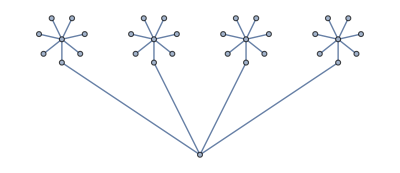

```mathematica
g=GraphData[{"BananaTree", {4, 8}}]
```

```mathematica
Graph[g,VertexLabels->Automatic]
```

Let’s perform a depth-first search on this tree

We start with the root node (33) in our case, and visit each node in the graph by first visiting all the children of a given node before visiting any of its siblings

```mathematica
rootNode=33;
```

We will need to find the neighbors of a given node:

```mathematica
AdjacencyList[g,rootNode]
```

We also don’t want to visit our parent, so we will use Cases and Except to skip items

```mathematica
AdjacencyList[g,1]
```

```mathematica
Cases[AdjacencyList[g,1],Except[33]]
```

```mathematica
depthFirst[graph_,node_,parent_]:=Module[{adj},
Print["Visiting ", node];
adj=Cases[AdjacencyList[graph,node],Except[parent]];
Scan[depthFirst[graph,#,node]&,adj]
]
depthFirst[graph_,root_]:=depthFirst[graph,root,root]
```

```mathematica
depthFirst[g,33]
```

```mathematica
DepthFirstScan[g,33,{"PrevisitVertex"->(Print["Visiting ",#]&)}];
```

```mathematica
BreadthFirstScan[g,33,{"PrevisitVertex"->(Print["Visiting ",#]&)}];
```

```mathematica
FindShortestPath[g,2,21]
```

```mathematica
g=Graph[PolyhedronData["Dodecahedron","SkeletonGraph"],VertexLabels->Automatic]
```

```mathematica
path=FindHamiltonianPath[g]
```

```mathematica
pg=PathGraph[path,VertexLabels->None,EdgeLabels->"Index"]
```

```mathematica
edgelabels=MapIndexed[#1->#2⟦1⟧&,EdgeList[pg]]
```

```mathematica
HighlightGraph[g,pg,VertexLabels->None,EdgeLabels->edgelabels]
```